# Analogue mécanique d’un spin 1/2

## Équation du mouvement du gyroscope : cas statique

0.00003164

42147.2

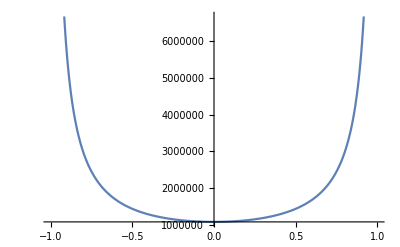

```mathematica
m = 0.345;
g = 9.81;
l = 31.25 * 10^(-3) ;
r = 53/2 *10^(-3);
e = 12 * 10^(-3);

J3 = 0.000055;
J1 = m*e^2/12 + J3/2


omegapsi = 200*Pi;
omegaphi = (m*g*l)/(J*omegapsi);
NombreAdd = ((J*omegapsi^2)/(m*g*l))^2
Lpsi = 0.5 *J* omega^2 ;
Lphi = Lpsi/NombreAdd; 


EnergieStatique[u_] = m*g*l*u + Lphi^2/(2 * J3) + (Lpsi - Lphi* u)^2 / (2 * J 1*(1-u^2));

Plot[EnergieStatique[u], {u, -1, 1 }]
```

```mathematica
FindMinimum[EnergieStatique[u],{u, 0}]
```

{9.40101×10^7,{u→2.69864×10^-7}}

```mathematica
m = 0.345;
g = 9.81;
l = 31.25 * 10^(-3) ;
J = 0.000055;
omegapsi = 200*Pi;
omegaphi = (m*g*l)/(J*omegapsi);
NombreAdd = ((J*omegapsi^2)/(m*g*l))^2
Lpsi = 0.5 *J* omega^2 ;
Lphi = Lpsi/NombreAdd; 


EnergieStatique[u_] = m*g*l*u + Lphi^2/(2 * J) + (Lpsi - Lphi* u)^2 / (2 * J *(1-u^2));
Plot[EnergieStatique[u], {u, -1, 1 }]
FindMinimum[EnergieStatique[u],{u, 0}]
```

42147.2

-Graphics-

{1.0715×10^6,{u→0.000023677}}

```mathematica
EnergieDynamique[u_, t_] = EnergieStatique[u_] + 1/2 * omega^2 * Cos[omega]
```

```mathematica
J3 =
```